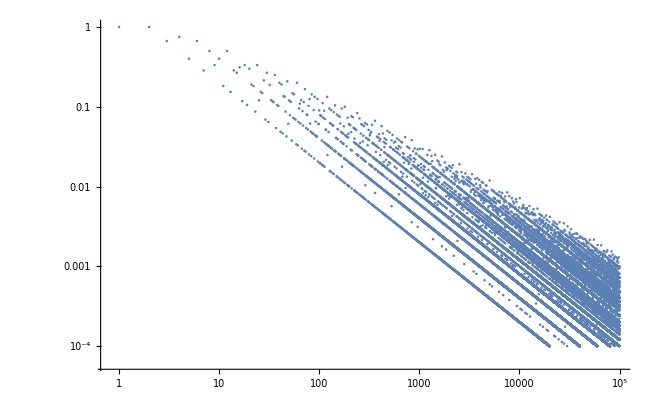

```mathematica
a=ToExpression[Import["/home/sid/Documents/School/Grade11-12/Courses/EE/codes/alldata"]];
plot=ListLogLogPlot[a]
```

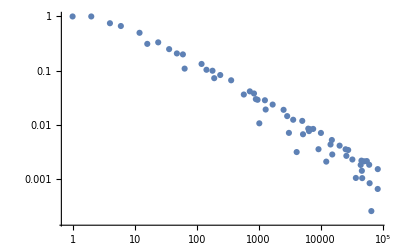

```mathematica
ListLogLogPlot[ToExpression[Import["/home/sid/Documents/School/Grade11-12/Courses/EE/codes/toprow"]]]
```

```mathematica
b=ToExpression[Import["/home/sid/Documents/School/Grade11-12/Courses/EE/codes/toprow"]];
refg = NonlinearModelFit[b,1/x^n,{n},x]
```

FittedModel[1/x^0.391579]

```mathematica
Manipulate[Show[ListLogLogPlot[b],LogLogPlot[refg[x]*x^j*k,{x,1,10^5}],Frame->True],{j,-1,1},{k,1,10}]
```

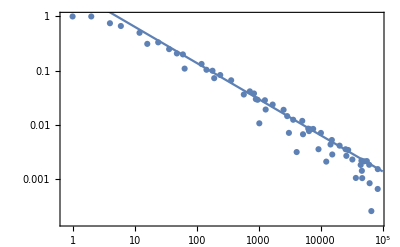

```mathematica
Show[ListLogLogPlot[b],LogLogPlot[x^(-2/3)*3,{x,1,10^5}],Frame->True]
```